```mathematica
A=Import["/home/sudhir/Ashish/latest/12,12sqrrndadj.txt","Table"];
```

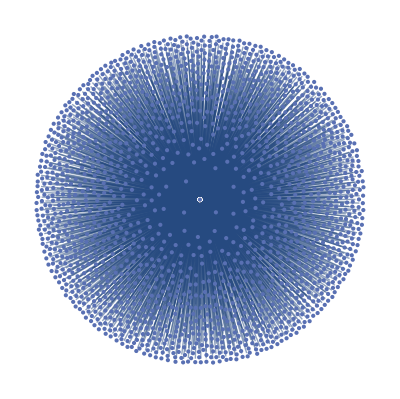

```mathematica
G1=AdjacencyGraph[A]
```

```mathematica
Q1=Import["/home/sudhir/Ashish/latest/12,12sqrrnddeg.txt","Table"];
```

```mathematica
Q=Q1-IdentityMatrix[1886];
```

```mathematica
f[x_]=((1-x^2)^(EdgeCount[G1]-VertexCount[G1]))*Det[IdentityMatrix[1886]-x*A+x*x*Q];
```

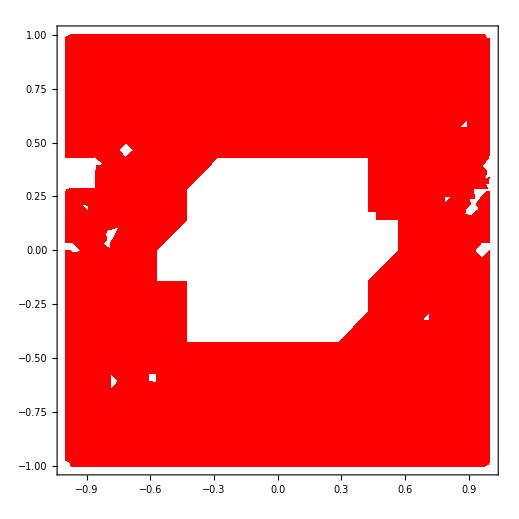

```mathematica
DensityPlot[1/Abs[f[xx+I*yy]],{xx,-1,1},{yy,-1,1},ColorFunction->Hue]
```

```mathematica
Plot3D[Abs[f[xx+I*yy]],{xx,-1,1},{yy,-1,1}]
```

-Graphics3D-

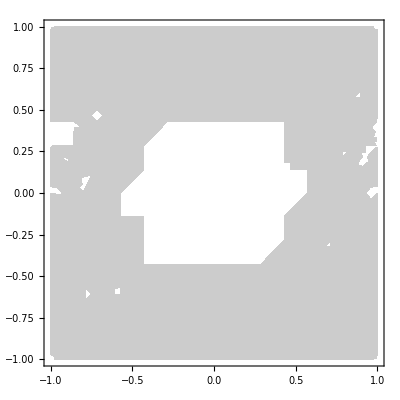

```mathematica
ContourPlot[1/Abs[f[xx+I*yy]],{xx,-1,1},{yy,-1,1}]
```